# Phase Transition under High-T Expansion

```mathematica
ClearAll["Global`*"]
```

```mathematica
WorkPath=SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Analytical Calculation

### Expression for critical temperature

This section calculates the formula for critical temperature.

```mathematica
$Assumptions={{Dterm,h,Eterm,T,λterm,T0}∈PositiveReals};
Vana=Dterm (T^2-T0^2)h^2-Eterm T h^3+λterm h^4;(*General form of high-T potential*)
hmin=h/.(Solve[D[Vana,h]==0,h]//Normal)[[2]]//Simplify(*Non-zero local minimum*)
Tcana=T/.Solve[(Vana/.{h->hmin}//Simplify)==0,T]//Normal//Simplify(*Critical temperature*)
hoverT=hmin/Tc/.{T->Tc}//Simplify
```

(3 Eterm T+√(9 Eterm^2 T^2+32 Dterm (-T^2+T0^2) λterm))/(8 λterm)

{2 T0 √((Dterm λterm)/(-Eterm^2+4 Dterm λterm))}

(3 Eterm Tc+√(9 Eterm^2 Tc^2+32 Dterm (T0^2-Tc^2) λterm))/(8 Tc λterm)

### Expression for eliminating S

```mathematica
$Assumptions={{Dterm,h,Eterm,T,λterm,T0,μH,A,μS,cs,S}∈PositiveReals};
VwithS=Dterm T^2 h^2-μH^2 h^2-Eterm T h^3+λterm h^4+1/2 μS^2 S^2-A(h^2+cs T^2)S;
Svev=S/.Solve[D[VwithS,S]==0,S]//Normal//Simplify
Dprime=Coefficient[VwithS/.{S->Svev},h,2]//Simplify
Eprime=Coefficient[VwithS/.{S->Svev},h,3]//Simplify
λprime=Coefficient[VwithS/.{S->Svev},h,4]//Simplify
VwithS/.{S->Svev}//Simplify
```

{(A (h^2+cs T^2))/μS^2}

{Dterm T^2-μH^2-(A^2 cs T^2)/μS^2}

{-Eterm T}

{λterm-A^2/(2 μS^2)}

{-Eterm h^3 T+h^2 (Dterm T^2+h^2 λterm-μH^2)-(A^2 (h^2+cs T^2)^2)/(2 μS^2)}

## Define V_eff in high-T with physical parameters

```mathematica
g=0.65;
gY=0.36;
yt=0.9945;
DSM=1/16(3 g^2+gY^2+4 yt^2);
ESM=1/(12π)(3/(√2)g^3+3/(2 √2)(g^2+gY^2)^(3/2));
cs=1/3;
mh=125.13;
GF = 1.16637 *10^-5;
v=1/(√(2 √2*GF));
μH2[mS_,sinθ_]:=(mh^2 mS^2)/(4(sinθ^2 mh^2+(1-sinθ^2)mS^2));
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(4 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(8 v^2);
VhighT[mS_,sinθ_,h_,T_]:=(DSM -A2[mS,sinθ]/μS2[mS,sinθ] cs)T^2 h^2-μH2[mS,sinθ] h^2-ESM T h^3+(λ[mS,sinθ]-A2[mS,sinθ]/(2μS2[mS,sinθ]))h^4;
T0[mS_,sinθ_]:=(√μH2[mS,sinθ])/(√(DSM-A2[mS,sinθ]/μS2[mS,sinθ] cs));
Tc[mS_,sinθ_]=(√(4(λ[mS,sinθ]-A2[mS,sinθ]/(2μS2[mS,sinθ]))(DSM -A2[mS,sinθ]/μS2[mS,sinθ] cs))T0[mS,sinθ])/(√(4(λ[mS,sinθ]-A2[mS,sinθ]/(2μS2[mS,sinθ]))(DSM -A2[mS,sinθ]/μS2[mS,sinθ] cs)-ESM^2));
Positive‵factor[mS_,sinθ_]=4(λ[mS,sinθ]-A2[mS,sinθ]/(2μS2[mS,sinθ]))(DSM -A2[mS,sinθ]/μS2[mS,sinθ] cs)-ESM^2;
strength[mS_,sinθ_]=ESM/(2(λ[mS,sinθ]-A2[mS,sinθ]/(2μS2[mS,sinθ])));
```

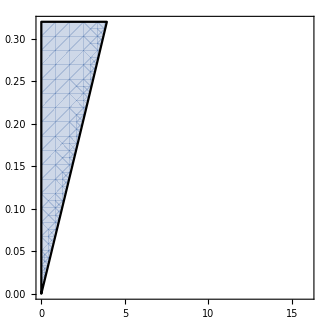

```mathematica
RegionPlot[4(λ[mS,sinθ]-A2[mS,sinθ]/(2μS2[mS,sinθ]))(DSM -A2[mS,sinθ]/μS2[mS,sinθ] cs)-ESM^2≤0,{mS,0,16},{sinθ,0,0.32}]
```

## Plots

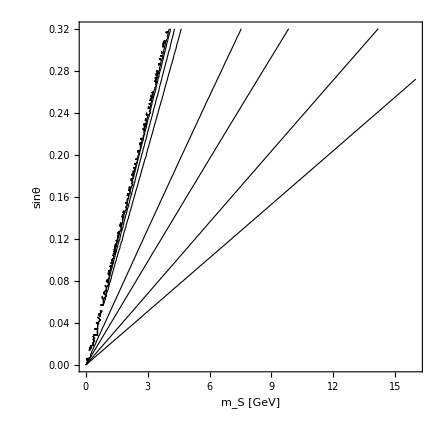

```mathematica
ContourPlot[Tc[mS,sinθ],{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},Contours->{25,30,40,50},ContourShading->None]
```

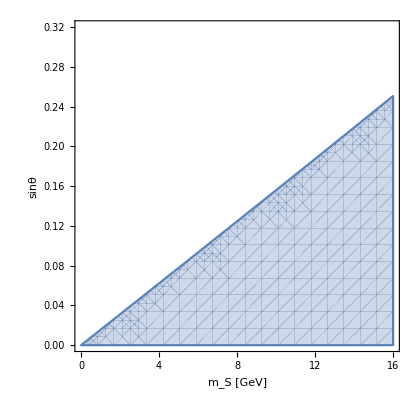

```mathematica
RegionPlot[strength[mS,sinθ]≤1.,{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},BoundaryStyle->ColorData[97,"ColorList"][[1]]]
```

## Output

```mathematica
DumpSave[WorkPath<>"/output/highT.m",{strength,Tc,Positive‵factor}];
```